### Calculate G numerically

#### H(t)

```mathematica
Ht[Nl_, centre_, A_, ω_, t_, ϕ_]:= Table[If[Abs[i-j]==1, -1, If[i==j &&i == centre, A*Cos[ω*t + ϕ], 0]], {i, 1, Nl}, {j, 1, Nl}]
Ht[7, 4, A, ω, t, ϕ] // MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | -1 | A Cos[ϕ+t ω] | -1 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

#### Linear full chain

```mathematica
HLin[Nl_, centre_, A_, ω_, t_, ϕ_]:= Table[If[Abs[i-j]==1, -1, If[i==j, i*A*Cos[ω*t + ϕ], 0]], {i, 1, Nl}, {j, 1, Nl}]
HLin[7, 4, A, ω, t, ϕ] // MatrixForm
```

(A Cos[ϕ+t ω] | -1 | 0 | 0 | 0 | 0 | 0
-1 | 2 A Cos[ϕ+t ω] | -1 | 0 | 0 | 0 | 0
0 | -1 | 3 A Cos[ϕ+t ω] | -1 | 0 | 0 | 0
0 | 0 | -1 | 4 A Cos[ϕ+t ω] | -1 | 0 | 0
0 | 0 | 0 | -1 | 5 A Cos[ϕ+t ω] | -1 | 0
0 | 0 | 0 | 0 | -1 | 6 A Cos[ϕ+t ω] | -1
0 | 0 | 0 | 0 | 0 | -1 | 7 A Cos[ϕ+t ω])

#### Density Evolution, create U(T)

```mathematica
(*Notes on indexing;
A python matrix of 51x51 is indexed 0 ->50
A mathematica matrix of size 51x51 is indexed 1->51
pythonMatrix[25] is the 26th row of the matrix. There are 25 rows on either side. 
mathematicaMatrix[26] is the 26th row of the matrix. There are 25 rows on either side. *)
```

```mathematica
nLat = 51; (*size of lattice*)
aA = 35;   (*time dependent potential parameters*)
centre = 26; (*site of oscillation*)
phis = {0, Pi/7, Pi/6, Pi/5, Pi/4, Pi/3, Pi/2};
filename = "analysis-G-mat-lin-35.csv";
username = "Georgia Nixon";
```

```mathematica
(*dataTable = {{"form", "a", "omega", "phi", "N", "hopping", "onsite", "next onsite", "NNN", "NNN overtop"}};*)
dataTable = Import["/Users/"<>username<>"/Code/MBQD/floquet-simulations/data/" <> filename,"Data"];
```

```mathematica
For[iP = 1, iP≤ 7, iP++,
ϕϕ = phis[[iP]];
Print[ϕϕ];

For[ ωω = 3.7, ωω ≤ 20, ωω += 0.1,
Print[ωω];
UT = Table[0, {i, 1, nLat},{j,1,nLat}];
T = 2π/ωω;
tf = T;

For[atomSiteStart=1,atomSiteStart≤nLat,atomSiteStart++,
ClearAll@ψ;
ψ0 = Table[If[i==atomSiteStart,1,0],{i,1,nLat}];
s=NDSolve[{-I *D[ψ[t], t]== HLin[nLat, centre, aA, ωω, t, ϕϕ].ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s]; 
ψT = Table[ψ[T][[1, i]], {i, 1, nLat}];
UT[[All, atomSiteStart]]= ψT
];
{eValsU, eVecs} = Eigensystem[UT];
eValsH = I*Log[eValsU] / T;
G = Chop[Sum[eValsH[[i]]*Outer[Times, eVecs[[i]], Conjugate[eVecs[[i]]]], {i, 1, nLat}]];
hopping = G[[centre,centre+1]];
onsite= G[[centre,centre]];
nextOnsite= G[[centre+1,centre+1]];
nnn= G[[centre,centre+2]];
nnnOvertop= G[[centre-1,centre+1]];
dataTable = Append[dataTable, {"Linear-m",Null, aA, ωω, N[ϕϕ], nLat, hopping, onsite, nextOnsite, nnn, nnnOvertop}];
];
Export["/Users/"<>username<>"/Code/MBQD/floquet-simulations/data/" <>filename,dataTable];
];
Export["/Users/"<>username<>"/Code/MBQD/floquet-simulations/data/" <> filename,dataTable];
```

0

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

π/7

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

π/6

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

π/5

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

π/4

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

π/3

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

π/2

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

```mathematica
Export["/Users/"<>username<>"/Code/MBQD/floquet-simulations/data/"<>filename,
{{"form","rtol","a","omega","phi","N","hopping","onsite","next onsite","NNN","NNN overtop"}}];
```

#### Plot G for certain conditions

```mathematica
(*Calculate G*)
```

```mathematica
nLat = 51; (*size of lattice*)
UT = Table[0, {i, 1, nLat},{j,1,nLat}];
centre = 26; aA = 35;  
ϕϕ = π/7; ωω = 9.6;
T = 2π/ωω;
tf = T;

For[atomSiteStart=1,atomSiteStart≤nLat,atomSiteStart++,
ClearAll@ψ;
ψ0 = Table[If[i==atomSiteStart,1,0],{i,1,nLat}];
s=NDSolve[{-I *D[ψ[t], t]== Ht[nLat, centre, aA, ωω, t, ϕϕ].ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s]; 
ψT = Table[ψ[T][[1, i]], {i, 1, nLat}];
UT[[All, atomSiteStart]]= ψT
];
{eValsU, eVecs} = Eigensystem[UT];
eValsH = I*Log[eValsU] / T;
G = Chop[Sum[eValsH[[i]]*Outer[Times, eVecs[[i]], Conjugate[eVecs[[i]]]], {i, 1, nLat}]];
```

A = 35, ω = 9.6, ϕ = π/7

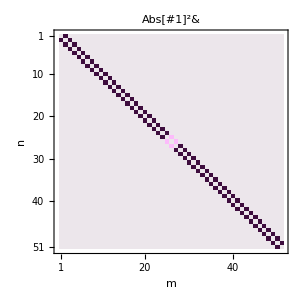
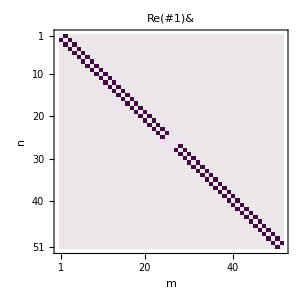
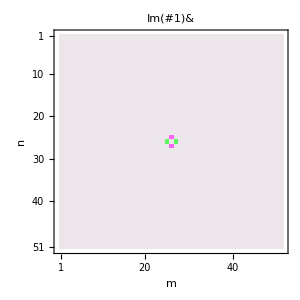

```mathematica
Print["A = ", aA, ", ω = ", ωω, ", ϕ = ", ϕϕ];Append[Table[MatrixPlot[f[G], FrameLabel->{"n","m"},   ImageSize-> {300,300}, ColorFunction->ColorData[{"GreenPinkTones", {-1, 1}}], ColorFunctionScaling->False, PlotLabel -> f], {f,{Abs[#]^2&,Re[#]&, Im[#]&}}], BarLegend[{"GreenPinkTones", {-1, 1}}]]
```

```mathematica
Export["/Users/Georgia/Code/MBQD/floquet-simulations/data/A35-w9p6-phpio7-G-mathematica-data.csv",G];
Export["/Users/Georgia/Code/MBQD/floquet-simulations/data/A35-w9p6-phpio7-G-mathematica-info.csv", 
{{"A", "omega", "phi/pi", "N", "centre"},
{aA, ωω, ϕϕ/π, nLat, centre }}];
```